```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
(*pi+result*)
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-pi-xi1-S1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;

dHerf=Interpolation[Flatten[dHeru,1]];
dHdaf=Interpolation[Flatten[dHdau,1]];

dEerf=Interpolation[Flatten[dEeru,1]];
dEdaf=Interpolation[Flatten[dEdau,1]];

dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-D-pi-xi1-S1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHerf=Interpolation[Flatten[dDHeru,1]];
dDHdaf=Interpolation[Flatten[dDHdau,1]];

dDEerf=Interpolation[Flatten[dDEeru,1]];
dDEdaf=Interpolation[Flatten[dDEdau,1]];
```

```mathematica
dgpdur=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-pi-xi1-S1-right.wdx"];
dHdgur=Query[1,1]@dgpdur;
dHerur=Query[1,2]@dgpdur;
dHdaur=Query[1,3]@dgpdur;
dEdgur=Query[2,1]@dgpdur;
dEerur=Query[2,2]@dgpdur;
dEdaur=Query[2,3]@dgpdur;

dHerfr=Interpolation[Flatten[dHerur,1]];
dHdafr=Interpolation[Flatten[dHdaur,1]];

dEerfr=Interpolation[Flatten[dEerur,1]];
dEdafr=Interpolation[Flatten[dEdaur,1]];

dDgpdur=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-j-dleta-D-pi-xi1-S1-right.wdx"];

dDHerur=Query[1,2]@dDgpdur;
dDHdaur=Query[1,3]@dDgpdur;

dDEerur=Query[2,2]@dDgpdur;
dDEdaur=Query[2,3]@dDgpdur;

dDHerfr=Interpolation[Flatten[dDHerur,1]];
dDHdafr=Interpolation[Flatten[dDHdaur,1]];

dDEerfr=Interpolation[Flatten[dDEerur,1]];
dDEdafr=Interpolation[Flatten[dDEdaur,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=0
Herall[x_,t_]:=dHerf[x,t]+dHdaf[x,t]+dHdafr[x,t]+dDHerf[x,t]+dDHdaf[x,t]+dDHdafr[x,t];
Edgall[x_,t_]:=0;
Eerall[x_,t_]:=dEerf[x,t]+dEdaf[x,t]+dEdafr[x,t]+dDEerf[x,t]+dDEdaf[x,t]+dDEdafr[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*Σ0 k+,只需要乘上系数，u=sbar=pi+的结果*)
Coep1=(1/(2*(2π)^4*fc^2))*(-c2);
(*k+的u贡献，分段但就是总的*)
k1Hdg[x_,t_]=Coep1*Hdgall[x,t];
k1Her[x_,t_]=Coep1*Herall[x,t];
k1Edg[x_,t_]=Coep1*Edgall[x,t];
k1Eer[x_,t_]=Coep1*Eerall[x,t];
(*k0没有u夸克*)
(*图的u夸克总结果，就是对粒子求和*)
Hdgzall[x_,t_]=k1Hdg[x,-t];
Herallwhole[x_,t_]=k1Her[x,-t];
Edgzall[x_,t_]=k1Edg[x,-t];
Eerallwhole[x_,t_]=k1Eer[x,-t];

(*d quark*)
(*k0的d夸克，与pi0不同输入没有1/2*)
ap0=0;
(*k0的d夸克，直接就是结果没有反转*)
k0Hdg[x_,t_]=ap0*Hdgall[x,t];
k0Her[x_,t_]=ap0*Herall[x,t];
k0Edg[x_,t_]=ap0*Edgall[x,t];
k0Eer[x_,t_]=ap0*Eerall[x,t];
(*图的d夸克总结果，就是对粒子求和*)
Hdgzalld[x_,t_]=k0Hdg[x,t];
Herallwholed[x_,t_]=k0Her[x,t];
Edgzalld[x_,t_]=k0Edg[x,t];
Eerallwholed[x_,t_]=k0Eer[x,t];
```

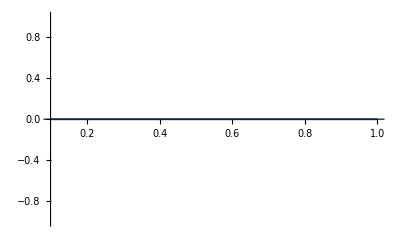

```mathematica
Plot[I*Hdgzall[x,-1],{x,0.1,1}]
```

```mathematica
Plot[I*Hdgfall[x,-1],{x,-1,-0.1}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {-0.0999959,1} lies outside the range of data in the interpolating function. Extrapolation will be used.

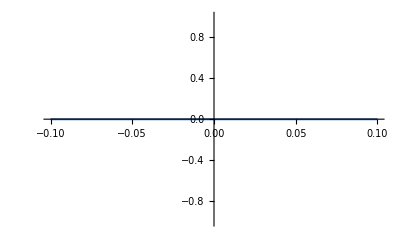

```mathematica
Plot[I*Herallwhole[x,-1],{x,-0.1,0.1}]
```

InterpolatingFunction::dmval: Input value {-0.0999959,1} lies outside the range of data in the interpolating function. Extrapolation will be used.

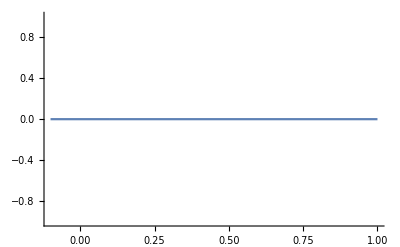

```mathematica
Show[Plot[I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

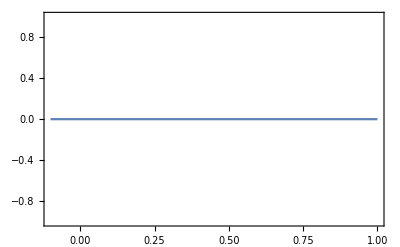
-Graphics-H_uxdiagram j

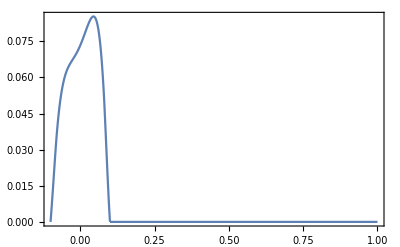
-Graphics-E_uxdiagram j

```mathematica
pHu2d=Labeled[Show[Plot[Hdgzall[x,1],{x,0.1,1},PlotRange->All],Plot[Herallwhole[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_u","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
pEu2d=Labeled[Show[Plot[Edgzall[x,1],{x,0.1,1},PlotRange->All],Plot[Eerallwhole[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_u","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
(*pathH=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"H-f-2d.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"E-f-2d.pdf"}];
```

```mathematica
(*Export[pathH,pHu2d]
```

```mathematica
(*Export[pathE,pEu2d]
```

```mathematica
(*s quark*)
```

```mathematica
(*k+,sbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
k1Hdgs[x_,t_]=-k1Hdg[-x,t];
k1Hers[x_,t_]=-k1Her[-x,t];
k1Edgs[x_,t_]=-k1Edg[-x,t];
k1Eers[x_,t_]=-k1Eer[-x,t];
(*k0,sbar=d*)
k0Hdgs[x_,t_]=-k0Hdg[-x,t];
k0Hers[x_,t_]=-k0Her[-x,t];
k0Edgs[x_,t_]=-k0Edg[-x,t];
k0Eers[x_,t_]=-k0Eer[-x,t];
(*图的总结果，就是对粒子求和*)
Hdgfalls[x_,t_]=k1Hdgs[x,t];
Herallwholes[x_,t_]=k1Hers[x,t];
Edgfalls[x_,t_]=k1Edgs[x,t];
Eerallwholes[x_,t_]=k1Eers[x,t];
```

```mathematica
pHd2d=Labeled[Show[Plot[Hdgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[Hdgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Herallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[Edgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Eerallwholed[x,-1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram j"},{Left,Bottom,Top},LabelStyle->24]
```

-Graphics-H_dxdiagram j

-Graphics-E_dxdiagram j

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-j-S.wdx"}];
pathd=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"d-diagram-j-S.wdx"}];
paths=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"s-diagram-j-S.wdx"}];
outu=<|"H"-><|"DGz"->Hdgzall[x,t],"ER"->Herallwhole[x,t],"DGf"->0|>,"E"-><|"DGz"->Edgzall[x,t],"ER"->Eerallwhole[x,t],"DGf"->0|>|>;
outd=<|"H"-><|"DGz"->Hdgzalld[x,t],"ER"->Herallwholed[x,t],"DGf"->0|>,"E"-><|"DGz"->Edgzalld[x,t],"ER"->Eerallwholed[x,t],"DGf"->0|>|>;
outs=<|"H"-><|"DGz"->0,"ER"->Herallwholes[x,t],"DGf"->Hdgfalls[x,t]|>,"E"-><|"DGz"->0,"ER"->Eerallwholes[x,t],"DGf"->Edgfalls[x,t]|>|>;
Export[pathu,outu]
Export[pathd,outd]
Export[paths,outs]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-j-S.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\d-diagram-j-S.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\s-diagram-j-S.wdx